```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
(*Summariz*)
(*y=f(x) 2D Plot ListPLot*)
(*z=f(x,y) 3D Plot3D ContourPlot DensityPlot*)
```

```mathematica
(*s=f(x,y,z) 4D ContourPlot3D*)
```

```mathematica
(*orbital-like function f(x,y,z)=A*g(r)h(y,z)*)
(*r=(x^2+y^2+z^2)*)

(*
       g      h

ls    e^-r    1
2 Subscript[P, z]   e^(-r/2)   z
3 Subscript[d, z^2]  e^(-r/3)   3 z^2 r^2
*)
```

```mathematica
r[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
f[x_,y_,z_]:=E^-r[x,y,z];
ContourPlot3D[f[x,y,z]==0.1,{x,-3,3},
{y,-3,3},{z,-3,3},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
f[x_,y_,z_]:=z*E^(-r[x,y,z]/2);
ContourPlot3D[{f[x,y,z]==0.1,f[x,y,z]==-0.1},{x,-10,10},
{y,-10,10},{z,-10,10},AxesLabel->{"x","y","z"},Mesh->None,
ContourStyle->{Directive[Green,Specularity[White,100]],
Directive[Yellow,Specularity[White,100]]}]
```

-Graphics3D-

```mathematica
f[x_,y_,z_]:=(3*z^2-r[x,y,z]^2)*E^(-r[x,y,z]/3);
ContourPlot3D[{f[x,y,z]==0.1,f[x,y,z]==-0.1},{x,-30,30},
{y,-30,30},{z,-30,30},AxesLabel->{"x","y","z"},Mesh->None,
ContourStyle->{Directive[Blue,Specularity[White,100]],Directive[Red,Specularity[White,100]]}]
```

-Graphics3D-

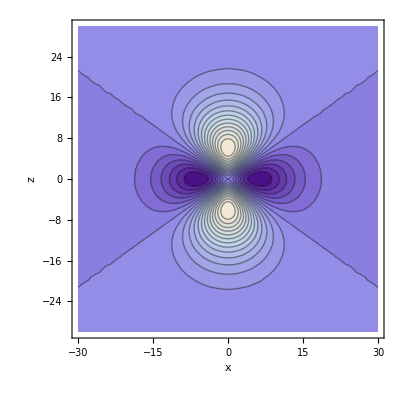

```mathematica
r[x_,z_]=Sqrt[x^2+z^2];
f[x_,z_]:=(3*z^2-r[x,z]^2)*E^(-r[x,z]/3);
ContourPlot[f[x,z],{x,-30,30},
{z,-30,30},FrameLabel->{"x","z"},PlotRange->All,
Contours->20]
```

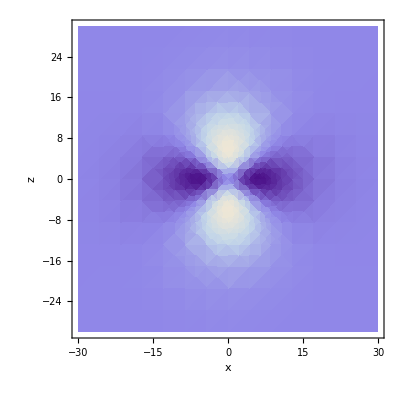

```mathematica
DensityPlot[f[x,z],{x,-30,30},
{z,-30,30},FrameLabel->{"x","z"},PlotRange->All]
```

```mathematica
(*
y=f(x)
f'(x)=dy/dx=_(h->0)^lim(f(x+h)-f(x))/h
*)
```

```mathematica
Clear[f]
```

```mathematica
f[x_]:=2*x^3+8*x^2-3*x+1;
```

```mathematica
f'[x]
```

-3+16 x+6 x^2

```mathematica
f'''[x]
```

12

```mathematica
f''''[x]
```

0

```mathematica
D[f[x],x]
```

-3+16 x+6 x^2

```mathematica
D[f[x],{x,2}]
```

16+12 x

```mathematica
(*
Subscript[((∂f)/(∂x)), y]=_(h->0)^lim(f(x+h,y)-f(x,y))/h
(∂^2 f)/(∂x^2),(∂^2 f)/(∂y^2),(∂^2 f)/(∂z^2)
*)
```

```mathematica
f[x_,y_]:=3*x^4-2*y^3+x^2*y^2;
D[f[x,y],x]
```

12 x^3+2 x y^2

```mathematica
D[f[x,y],{x,2}]
```

36 x^2+2 y^2

```mathematica
D[f[x,y],x,y,x]
```

4 y

```mathematica
(*
OverHat[Subscript[P, x]]=ℏ/i d/dx;
ℏ=h/(2π);
K̂=OverHat[Subscript[P, x]]^2/(2m)=-η^2/(2m)d^2/(d^2 x);
Subscript[ϕ, h](λ)=(2/L)^(1/2)sin(nπx/L);
*)
```

```mathematica
ψ[x_]:=(2/L)^(1/2)*Sin[n*π*x/L];
(ℏ/I)*D[ψ[x],x]
```

-ⅈ √2 (1/L)^(3/2) n π ℏ Cos[(n π x)/L]

```mathematica
-ℏ^2/(2m)*D[ψ[x],{x,2}]
```

((1/L)^(5/2) n^2 π^2 ℏ^2 Sin[(n π x)/L])/(√2 m)

```mathematica
(*
thermodynamic;
α=1/V Subscript[((∂V)/(∂T)), P];
Subscript[K, T]=-1/V Subscript[((∂V)/(∂P)), T];
PV=nRT;
*)
```

```mathematica
v[t_,p_]:=n*R*t/p;
(1/v)*D[v[t,p],t]
```

(n R)/(p v)

```mathematica
(-1/v)*D[v[t,p],p]
```

(n R t)/(p^2 v)